```mathematica
(* ******** CODE FOR GENERATING FIGS. 4, 5 AND 6 ********  *)
```

```mathematica
SetOptions[MaTeX,"Preamble"->{"\\usepackage{color}"}];
```

```mathematica
uini = 0.5;
kini = 1.0;

km =4;
```

```mathematica
(* A -> Vertex O. B -> Vertex P, C -> Vertex N *)
(* THE NOP PROTOCOL IS OBTAINED IN A DIFFERENT WAY NUMERICALLY, SINCE IT SEEMS TO BE HARDER TO DEAL WITH *)
```

```mathematica
tfCAB[x_,y_]:=Piecewise[{{Min[tf/.NSolve[{1/(x+y)==(1/(kini+uini)+2*tf)*u^2,1/(x-y)==w^2/(kini-uini)+2*(tf),1/x==(w/kini+2*tf)*u,u>0,u<1,w>0,w<1},{tf,w,u}][[2]],tf/.NSolve[{1/(x+y)==(1/(kini+uini)+2*tf)*u^2,1/(x-y)==w^2/(kini-uini)+2*(tf),1/x==(w/kini+2*tf)*u,u>0,u<1,w>0,w<1},{tf,w,u}][[1]]],Length[NSolve[{1/(x+y)==(1/(kini+uini)+2*tf)*u^2,1/(x-y)==w^2/(kini-uini)+2*(tf),1/x==(w/kini+2*tf)*u,u>0,u<1,w>0,w<1},{tf,w,u}]]>1.5},{tf/.NSolve[{1/(x+y)==(1/(kini+uini)+2*tf)*u^2,1/(x-y)==w^2/(kini-uini)+2*(tf),1/x==(w/kini+2*tf)*u,u>0,u<1,w>0,w<1},{tf,w,u}][[1]],1.5>Length[NSolve[{1/(x+y)==(1/(kini+uini)+2*tf)*u^2,1/(x-y)==w^2/(kini-uini)+2*(tf),1/x==(w/kini+2*tf)*u,u>0,u<1,w>0,w<1},{tf,w,u}]]>0.5},{{},Length[NSolve[{1/(x+y)==(1/(kini+uini)+2*tf)*u^2,1/(x-y)==w^2/(kini-uini)+2*(tf),1/x==(w/kini+2*tf)*u,u>0,u<1,w>0,w<1},{tf,w,u}]]<0.5}}]
```

```mathematica
vec={};
ϵk=0.02;
ϵu=0.0025;
For[i=1,i<201,i++,
k=ϵk*i;
Nsteps=uini*k/ϵu;
uvar=Select[Table[{ϵu*j,tfCAB[k,ϵu*j]},{j,0,Nsteps}],UnsameQ[#[[2]],{}] &][[1]][[1]]; 
AppendTo[vec,{k,uvar}];
Print[k]
]
```

```mathematica
Export["file path for 'tfNOP.dat'",vec]
```

```mathematica
(* THE ABOVE ALLOWS TO OBTAIN THE 'tfNOP.dat' FILE. THE FOLLOWING DEALS DIRECTLY WITH THE PLOTS FROM THE FIGURES *)
```

```mathematica
vec = Import["file path for 'tfNOP.dat'"];
uNOP=Interpolation[vec];
```

```mathematica
ui=0.5;
ξ=(1-ui)/(1+ui);

ufunOP[k_]:=u/.NSolve[{√(1/(k+u))*(1/(k-u)-ui/(1-ui))==1/k*√(1/(k-u)-(2ui)/(1-ui^2)),u/(k^2-u^2)>ui/(1-ui^2),u/(k(k-u))>ui/(1-ui),1/(k-u)>(2ui)/(1-ui^2),1/(k-u)>1/(1-ui)},u];
ufunPO1[k_]:=u/.NSolve[{√((1+ui)*((-2u)/(k^2-u^2)+1/(1-ui)))==(-u/(k*(k-u))+1/(1-ui)),u<k,1/(1-ui)>u/(k*(k-u)),1/(1-ui)>(2u)/(k^2-u^2),1/(k-u)>1/(1-ui),u>0},u][[1]];
ufunPO2[k_]:=u/.NSolve[{√((1+ui)*((-2u)/(k^2-u^2)+1/(1-ui)))==(-u/(k*(k-u))+1/(1-ui)),u<k,1/(1-ui)>u/(k*(k-u)),1/(1-ui)>(2u)/(k^2-u^2),1/(k-u)>1/(1-ui),u>0},u][[2]];
ufunPO3[k_]:=u/.NSolve[{√((1+ui)*((-2u)/(k^2-u^2)+1/(1-ui)))==(-u/(k*(k-u))+1/(1-ui)),u<k,1/(1-ui)>u/(k*(k-u)),1/(1-ui)>(2u)/(k^2-u^2),1/(k-u)>1/(1-ui),u>0},u][[3]];
ufunON[k_]:=u/.NSolve[{√(1/(k-u))*(1/(k+u)+ui/(1+ui))==1/k*√(1/(k+u)+(2ui)/(1-ui^2)),u/(k^2-u^2)<ui/(1-ui^2),u/(k(k+u))<ui/(1+ui),1/(k+u)>(-2ui)/(1-ui^2),1/(k+u)>1/(1+ui),u<0},u];
ufunNO1[k_]:=u/.NSolve[{√((1-ui)*((2u)/(k^2-u^2)+1/(1+ui)))==(u/(k*(k+u))+1/(1+ui)),u<k,1/(1+ui)>-u/(k*(k+u)),1/(1+ui)>(-2u)/(k^2-u^2),1/(k+u)>1/(1+ui),u<0},u][[1]];
ufunNO2[k_]:=u/.NSolve[{√((1-ui)*((2u)/(k^2-u^2)+1/(1+ui)))==(u/(k*(k+u))+1/(1+ui)),u<k,1/(1+ui)>-u/(k*(k+u)),1/(1+ui)>(-2u)/(k^2-u^2),1/(k+u)>1/(1+ui),u<0},u][[2]];
ufunNO3[k_]:=u/.NSolve[{√((1-ui)*((2u)/(k^2-u^2)+1/(1+ui)))==(u/(k*(k+u))+1/(1+ui)),u<k,1/(1+ui)>-u/(k*(k+u)),1/(1+ui)>(-2u)/(k^2-u^2),1/(k+u)>1/(1+ui),u<0},u][[3]];
ufunPN[k_]:=Abs[ui]*k;
```

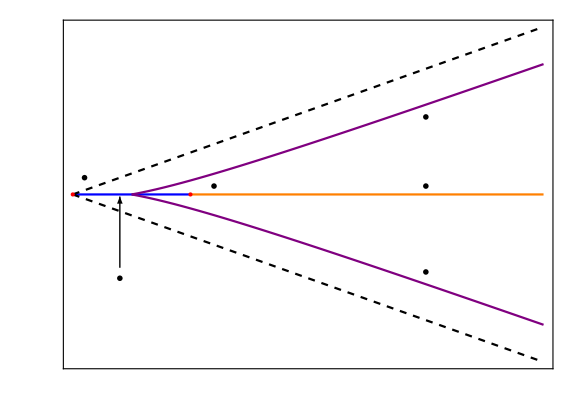

```mathematica
(* FIG. 4 (LEFT) *)

u0fun[k_,σ_]:=σ*k*(2*k-1)/(2*k+1);
Show[Plot[{0},{k,0,1},PlotStyle->Blue],Plot[{0},{k,1,kmax},PlotStyle->Orange],Plot[{u0fun[k,1],u0fun[k,-1]},{k,0.5,kmax},PlotStyle->Purple],Plot[{k},{k,0,kmax},PlotStyle->{Black,Dashed}],Plot[{-k},{k,0,kmax},PlotStyle->{Black,Dashed}],Frame->True,FrameStyle->Directive[Black,28,FontFamily->"Times New Roman"],FrameLabel->MaTeX[{"k_f","u_f"},Magnification->2],ImageSize->Large,AspectRatio->0.7,PlotRange->{{0,kmax},{-kmax,kmax}},FrameTicks->{{Table[{2*i,MaTeX[NumberForm[2*i,{1,1}],Magnification->2]},{i,-2,2}],None},{Table[{1*i,MaTeX[NumberForm[1*i,{2,1}],Magnification->2]},{i,0,5}],None}},Axes->False,Epilog->{{PointSize[Large],Directive[Red],Point[{1,0}]},{PointSize[Large],Directive[Red],Point[{0,0}]},Inset[MaTeX["\\text{OP} / \\text{ON}",Magnification->1.5],{0.4,-2}],{Arrow[{{0.4,-1.75},{0.4,-0.05}}]},Inset[MaTeX["\\text{PN} / \\text{NP}",Magnification->1.5],{3,0.2}],Inset[MaTeX["\\text{PO}",Magnification->1.5],{3,1.85}],Inset[MaTeX["\\text{NO}",Magnification->1.5],{3,-1.85}],Inset[MaTeX["\\textcolor{red}{\\text{O}}",Magnification->1.5],{0.1,0.4}],Inset[MaTeX["\\textcolor{red}{\\text{I}}",Magnification->1.5],{1.2,0.2}]},PlotRangePadding->None ]
```

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

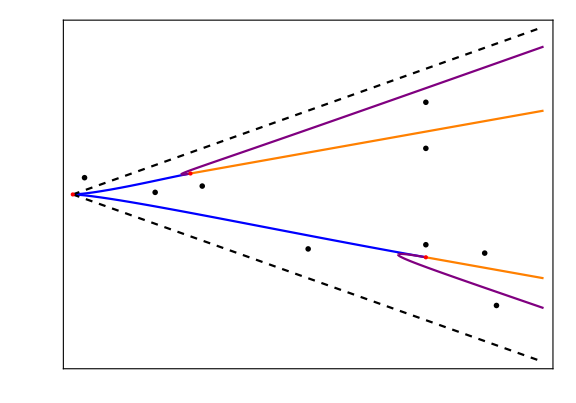

```mathematica
(* FIG. 4 (RIGHT) *)

Show[Plot[{ufunOP[k]},{k,0,kmax},PlotStyle->Blue],Plot[{ufunPN[k]},{k,1,kmax},PlotStyle->Orange],Plot[{-ufunPN[k]},{k,3,kmax},PlotStyle->Orange],Plot[{ufunON[k]},{k,0,kmax},PlotStyle->Blue],Plot[{ufunPO1[k],ufunPO2[k],ufunPO3[k]},{k,0,kmax},PlotStyle->Purple],Plot[{ufunNO1[k],ufunNO2[k],ufunNO3[k]},{k,0,kmax},PlotStyle->Purple],Plot[{k},{k,0,kmax},PlotStyle->{Black,Dashed}],Plot[{-k},{k,0,kmax},PlotStyle->{Black,Dashed}],Frame->True,FrameStyle->Directive[Black,28,FontFamily->"Times New Roman"],FrameLabel->MaTeX[{"k_f","u_f"},Magnification->2],ImageSize->Large,AspectRatio->0.7,PlotRange->{{0,kmax},{-kmax,kmax}},FrameTicks->{{Table[{2*i,MaTeX[NumberForm[2*i,{1,1}],Magnification->2]},{i,-10,10}],None},{Table[{1*i,MaTeX[NumberForm[1*i,{2,1}],Magnification->2]},{i,0,10}],None}},Axes->False,Epilog->{{PointSize[Large],Directive[Red],Point[{1,ui}]},{PointSize[Large],Directive[Red],Point[{0,0}]},{PointSize[Large],Directive[Red],Point[{1/ξ,-ui/ξ}]},Inset[MaTeX["\\text{OP}",Magnification->1.5],{0.7,0.05}],Inset[MaTeX["\\text{PO}",Magnification->1.5],{3,2.2}],Inset[MaTeX["\\text{PN} / \\text{NP}",Magnification->1.5],{3,1.1}],Inset[MaTeX["\\text{PN} / \\text{NP}",Magnification->1.5],{3.5,-1.4}],Inset[MaTeX["\\text{NO}",Magnification->1.5],{3.6,-2.65}],Inset[MaTeX["\\text{ON}",Magnification->1.5],{2,-1.3}],Inset[MaTeX["\\textcolor{red}{\\text{O}}",Magnification->1.5],{0.1,0.4}],Inset[MaTeX["\\textcolor{red}{\\text{I}}",Magnification->1.5],{1.1,0.2}],Inset[MaTeX["\\textcolor{red}{\\text{N}^*}",Magnification->1.5],{3,-1.2}]},PlotRangePadding->None ]
```

```mathematica
(* FIG. 5 *)

uini=0.5;
p1=Show[RegionPlot[DiscretizeRegion[ImplicitRegion[y<x &&2*x^2*tf1[x,y,kini,uini]>x+y && y>0,{x,y}],{{0,km},{-km,km}}],PlotStyle->LightRed,BoundaryStyle->None,PlotLegends->MaTeX[{"\\text{OPO}"},Magnification->1.5]],RegionPlot[DiscretizeRegion[ImplicitRegion[y/(x^2-y^2)>uini/(kini^2-uini^2)&& y<x  && y > -x &&  kini-uini > x - y &&y/(x*(x-y))>uini/(kini*(kini-uini)) && (kini+uini)/(x+y)-2*(kini+uini)*tf1[x,y,kini,uini]<(kini/x-2*kini*tf1[x,y,kini,uini])^2 && (x+y)/(kini+uini)+2*(x+y)*tf1[x,y,kini,uini]<(x/kini+2*x*tf1[x,y,kini,uini])^2 && 2*x^2*tf1[x,y,kini,uini]<x+y,{x,y}],{{0,km},{-km,km}}],Axes->True,PlotStyle->LightOrange,BoundaryStyle->None,PlotLegends->MaTeX[{"\\text{OPO / POP}"},Magnification->1.5]],RegionPlot[DiscretizeRegion[ImplicitRegion[y<x &&2*x^2*tf1[x,y,kini,uini]<x+y && y>0 && kini^2*(x^2-y^2)<x^2*(kini^2-uini^2),{x,y}],{{0,km},{-km,km}}],PlotStyle->LightYellow,BoundaryStyle->None,PlotLegends->MaTeX[{"\\text{PON}"},Magnification->1.5]],RegionPlot[DiscretizeRegion[ImplicitRegion[y/(x^2-y^2)>uini/(kini^2-uini^2)&& y<x  && y > -x &&  kini-uini > x - y &&y/(x*(x-y))>uini/(kini*(kini-uini)) && (kini+uini)/(x+y)-2*(kini+uini)*tf1[x,y,kini,uini]<(kini/x-2*kini*tf1[x,y,kini,uini])^2 && (x+y)/(kini+uini)+2*(x+y)*tf1[x,y,kini,uini]<(x/kini+2*x*tf1[x,y,kini,uini])^2 && 2*x^2*tf1[x,y,kini,uini]<x+y,{x,y}],{{0,km},{-km,km}}],Axes->True,PlotStyle->LightOrange,BoundaryStyle->None],RegionPlot[y/(x^2-y^2)<uini/(kini^2-uini^2)&& y>uNOP[x] &&  kini^2*(x^2-y^2)>x^2*(kini^2-uini^2),{x,0,km},{y,-km,km},PlotPoints->100,PlotStyle->LightGreen,BoundaryStyle->None,PlotLegends->MaTeX[{"\\text{NOP}"},Magnification->1.5]],RegionPlot[kini^2*(x^2-y^2)<x^2*(kini^2-uini^2) && (1/x-1/(x+y)+1/(1+ui))^2*(1/(1-ui))<(1/(x-y)-1/(x+y)+1/(1+ui)) && y<0,{x,0,km},{y,-km,km},PlotStyle->LightGreen,BoundaryStyle->None,PlotPoints->100],RegionPlot[ (1/x-1/(x+y)+1/(1+ui))^2*(1/(1-ui))>(1/(x-y)-1/(x+y)+1/(1+ui)) && kini^2*(x^2-y^2)<x^2*(kini^2-uini^2)&&y<0  && x+y>1+ui,{x,0,km},{y,-km,km},PlotStyle->LightGreen,PlotPoints->100,BoundaryStyle->None],RegionPlot[y<uNOP[x] &&  kini^2*(x^2-y^2)>x^2*(kini^2-uini^2) && 2*tf2[x,y,kini,uini]<(x-y)/x^2&& kini^2*(kini+uini)*y^2<x^2*(x+y)*uini^2,{x,0,km},{y,-km,km},PlotPoints->100,PlotStyle->LightCyan,BoundaryStyle->None,PlotLegends->MaTeX[{"\\text{ONP / OPN}"},Magnification->1.5]],RegionPlot[(1/x)^2*(1/(1-ui)+1/(x+y)-1/(1+ui))>(1/(x-y))*(1+1/(x+y)-1/(1+ui))^2&& y<x && y>-x && y<0 &&kini^2*(kini+uini)*y^2>x^2*(x+y)*uini^2,{x,0,km},{y,-km,km},PlotPoints->100,PlotStyle->LightBlue,BoundaryStyle->None,PlotLegends->MaTeX[{"\\text{NON}"},Magnification->1.5]],RegionPlot[ (1/x-1/(x+y)+1/(1+ui))^2*(1/(1-ui))>(1/(x-y)-1/(x+y)+1/(1+ui)) && y<0 && y>-x && (1/x)^2*(1/(1-ui)+1/(x+y)-1/(1+ui))<(1/(x-y))*(1+1/(x+y)-1/(1+ui))^2 && x+y<1+ui &&  2*tf2[x,y,kini,uini]<(x-y)/x^2,{x,0,km},{y,-km,km},PlotPoints->200,PlotStyle->LightPurple, BoundaryStyle->None,PlotLegends->MaTeX[{"\\text{ONO / NON}"},Magnification->1.5]],RegionPlot[ 2*tf2[x,y,kini,uini]>(x-y)/x^2 && y<0 && y>-x,{x,0,km},{y,-km,0},PlotStyle->LightMagenta,BoundaryStyle->None,PlotPoints->100,PlotLegends->MaTeX[{"\\text{ONO}"},Magnification->1.5]],Plot[{ufunOP[k]},{k,0,kmax},PlotStyle->Blue],Plot[{ufunPN[k]},{k,1,kmax},PlotStyle->Orange],Plot[{-ufunPN[k]},{k,3,kmax},PlotStyle->Orange],Plot[{ufunON[k]},{k,0,kmax},PlotStyle->Blue],Plot[{ufunPO1[k],ufunPO2[k],ufunPO3[k]},{k,0,kmax},PlotStyle->Purple],Plot[{ufunNO1[k],ufunNO2[k],ufunNO3[k]},{k,0,kmax},PlotStyle->Purple],Plot[{k},{k,0,kmax},PlotStyle->{Black,Dashed}],Plot[{-k},{k,0,kmax},PlotStyle->{Black,Dashed}],ListLinePlot[vec,PlotStyle->{DotDashed,Black}],ContourPlot[ 2*x^2*tf1[x,y,kini,uini]==x+y,{x,0,km},{y,0,x},ContourStyle->{Black,DotDashed}],ContourPlot[2*tf2[x,y,kini,uini]==(x-y)/x^2,{x,0,km},{y,-x,0},ContourStyle->{Black,DotDashed}],ContourPlot[kini^2*(kini+uini)*y^2==x^2*(x+y)*uini^2,{x,0,1/ξ},{y,-x,0},ContourStyle->{Black,DotDashed}],Frame->True,FrameStyle->Directive[Black,28,FontFamily->"Times New Roman"],FrameLabel->MaTeX[{"k_f","u_f"},Magnification->2],ImageSize->Large,AspectRatio->0.7,PlotRange->{{0,kmax},{-kmax,kmax}},FrameTicks->{{Table[{2*i,MaTeX[NumberForm[2*i,{1,1}],Magnification->2]},{i,-10,10}],None},{Table[{1*i,MaTeX[NumberForm[1*i,{2,1}],Magnification->2]},{i,0,10}],None}},Axes->False,Epilog->{{PointSize[Large],Directive[Red],Point[{1,ui}]},{PointSize[Large],Directive[Red],Point[{0,0}]},{PointSize[Large],Directive[Red],Point[{1/ξ,-ui/ξ}]},Inset[MaTeX["\\textcolor{red}{\\text{O}}",Magnification->1.5],{0.1,0.4}],Inset[MaTeX["\\textcolor{red}{\\text{I}}",Magnification->1.5],{1.1,0.1}],Inset[MaTeX["\\textcolor{red}{\\text{N}^*}",Magnification->1.5],{3,-1.2}]},PlotRangePadding->None]
```

InterpolatingFunction::dmval: Input value {0.0000404444} lies outside the range of data in the interpolating function. Extrapolation will be used.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

```mathematica
Export["file path for 'two_bang_map.pdf'",p1]
```

Power::infy: Infinite expression 1/0. encountered.

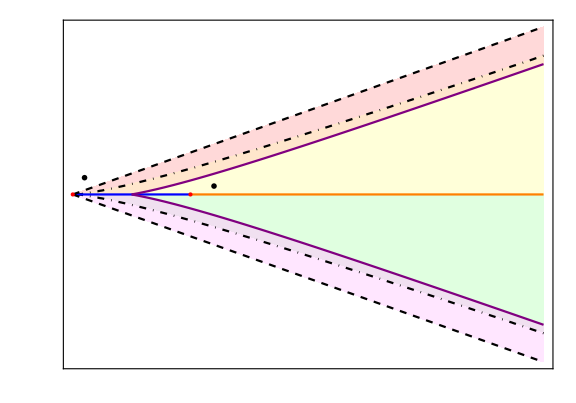

```mathematica
(* FIG. 6 *)

p2=Show[RegionPlot[2*tf1[x,y,kini,0]>(x+y)/x^2 && y<x && y>0,{x,0,km},{y,-km,km},PlotStyle->LightRed,BoundaryStyle->None,PlotLegends->MaTeX[{"\\text{OPO}"},Magnification->1.5],PlotPoints->100],RegionPlot[2*tf1[x,y,kini,0]<(x+y)/x^2 && y>x*(2*x-1)/(2*x+1)&& y<x && y>0,{x,0,km},{y,-km,km},PlotStyle->LightOrange,BoundaryStyle->None,PlotLegends->MaTeX[{"\\text{OPO / POP}"},Magnification->1.5],PlotPoints->200],RegionPlot[y<x*(2*x-1)/(2*x+1)&& y<x && y>0,{x,0,km},{y,-km,km},PlotStyle->LightYellow,BoundaryStyle->None,PlotLegends->MaTeX[{"\\text{PON}"},Magnification->1.5],PlotPoints->100],RegionPlot[y>-x*(2*x-1)/(2*x+1)&& y<x && y<0,{x,0,km},{y,-km,km},PlotStyle->LightGreen,BoundaryStyle->None,PlotLegends->MaTeX[{"\\text{NOP}"},Magnification->1.5],PlotPoints->100],RegionPlot[2*tf2[x,y,kini,0]<(x-y)/x^2 && y<-x*(2*x-1)/(2*x+1)&& y<x && y<0 && y>-x,{x,0,km},{y,-km,km},PlotStyle->LightPurple,BoundaryStyle->None,PlotLegends->MaTeX[{"\\text{ONO / NON}"},Magnification->1.5],PlotPoints->200],RegionPlot[2*tf2[x,y,kini,0]>(x-y)/x^2 && y>-x && y<0,{x,0,km},{y,-km,km},PlotStyle->LightMagenta,BoundaryStyle->None,PlotLegends->MaTeX[{"\\text{ONO}"},Magnification->1.5],PlotPoints->100],ContourPlot[ 2*tf2[x,y,kini,0]==(x-y)/x^2,{x,0,km},{y,-km,0},ContourStyle->{Black,DotDashed}],ContourPlot[ 2*tf1[x,y,kini,0]==(x+y)/x^2,{x,0,km},{y,0,km},ContourStyle->{Black,DotDashed}],Plot[{0},{k,0,1},PlotStyle->Blue],Plot[{0},{k,1,km},PlotStyle->Orange],Plot[{u0fun[k,1],u0fun[k,-1]},{k,0.5,km},PlotStyle->Purple],Plot[{k},{k,0,km},PlotStyle->{Black,Dashed}],Plot[{-k},{k,0,km},PlotStyle->{Black,Dashed}],Frame->True,FrameStyle->Directive[Black,28,FontFamily->"Times New Roman"],FrameLabel->MaTeX[{"k_f","u_f"},Magnification->2],ImageSize->Large,AspectRatio->0.7,PlotRange->{{0,km},{-km,km}},FrameTicks->{{Table[{2*i,MaTeX[NumberForm[2*i,{1,1}],Magnification->2]},{i,-2,2}],None},{Table[{1*i,MaTeX[NumberForm[1*i,{2,1}],Magnification->2]},{i,0,5}],None}},Axes->False,Epilog->{{PointSize[Large],Directive[Red],Point[{1,0}]},{PointSize[Large],Directive[Red],Point[{0,0}]},Inset[MaTeX["\\textcolor{red}{\\text{O}}",Magnification->1.5],{0.1,0.4}],Inset[MaTeX["\\textcolor{red}{\\text{I}}",Magnification->1.5],{1.2,0.2}]},PlotRangePadding->None]
```

```mathematica
Export["file path for 'two_bang_map_ui0.pdf'",p2]
```